# N30 Integral

### Parameters

```mathematica
(* a = 3 *)pbarRoot = {0.299618729049241,0.701981065353977,1.24974569814569,1.94514382443706,2.78994869155499,3.78614305529879,4.93605293430173,6.24240692441721,7.70838362900271,9.3376617765878,11.1344784990019,13.1036993239838,15.2509033992287,17.5824881879873,20.1057991514724,22.8292918399089,25.7627366009885,28.9174802233293,32.3067850039226,35.9462752181738,39.8545359681502,44.0539338428991,48.5717701879893,53.4419507581545,58.7074908793654,64.4244418290391,70.6683893377061,77.5459900633602,85.2174664086695,93.9467116599065,104.238552969691,117.391742318923};

pbarWeight={0.00660146448073508,0.0813584931042281,0.347537436309438,0.809963198105261,1.22739584119905,1.32050782861975,1.06049919505728,0.655616488144915,0.318173017008472,0.122743109012855,0.0379333897858022,0.00943187028689987,0.00188978713293874,0.000304914974586437,3.95130877631855*10^-05,4.09377958251348*10^-06,3.36921618654073*10^-07,2.1841295448875*10^-08,1.10337736506627*10^-09,4.28638379146177*10^-11,1.25966453444067*10^-12,2.74423030367617*10^-14,4.32175197361363*10^-16,4.76686817705967*10^-18,3.53643350342934*10^-20,1.67355018349782*10^-22,4.70254099995936*10^-25,7.09116556196869*10^-28,4.93082516196282*10^-31,1.23284946609868*10^-34,6.91389702736573*10^-39,2.63586492716958*10^-44};

GeVinversefm = 5.067731;

μBpts = 100;
Tpts = 100;

μBmin = 0.0;
μBmax = 4.06;
dμB=(μBmax-μBmin)/μBpts;
μBgrid=Table[μBmin+(i-1)*dμB,{i,1,μBpts+1}];

Tmin = 0.1;
Tmax = 0.82;
dT=(Tmax-Tmin)/Tpts;
Tgrid=Table[Tmin+(i-1)*dT,{i,1,Tpts+1}];
```

## Baryon

### Proton

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

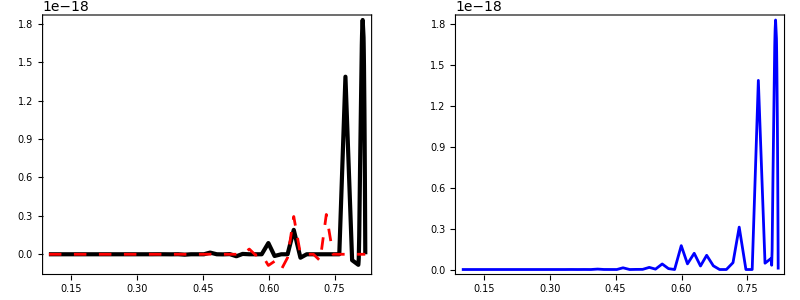

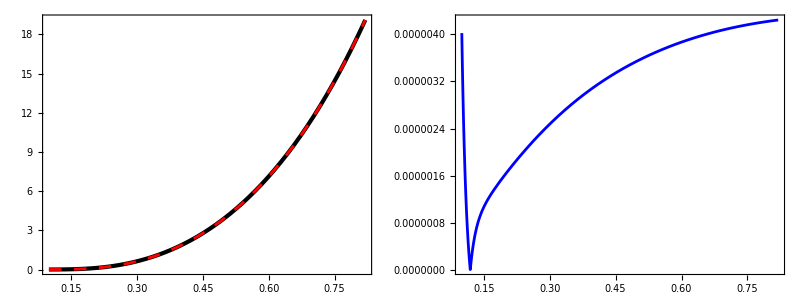

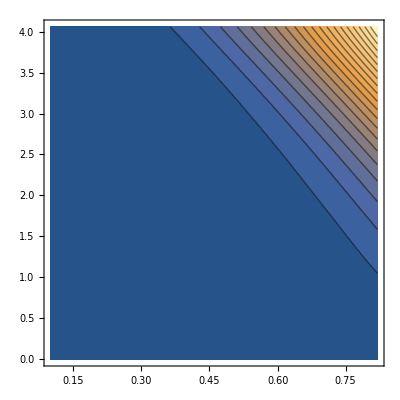

```mathematica
m = 0.938*GeVinversefm;
dof = 2.0;
θ=1.0;
N30Integrand[T_,μB_,pbar_]:=(dof*(T)^5)/(2.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(2/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
N30GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^5)/(2.0*Pi^2)*(pbar)^-1*((pbar)^2+(m/T)^2)^(2/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

N30=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[N30Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N30Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*N30GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N30=Interpolation[N30];
N30Gauss=Interpolation[N30Gauss];
GraphicsGrid[{{Plot[{N30[T,μBmin],N30Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N30[T,μBmin]-N30Gauss[T,μBmin])]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{N30[T,μBmax],N30Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N30[T,μBmax]-N30Gauss[T,μBmax])/N30Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(N30[T,μB]-N30Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(N30[T,μB]-N30Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Lambda

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

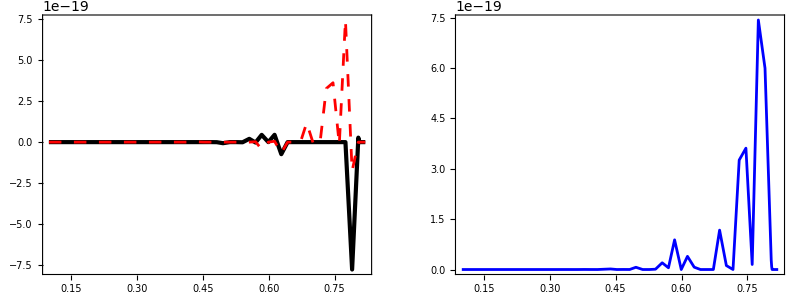

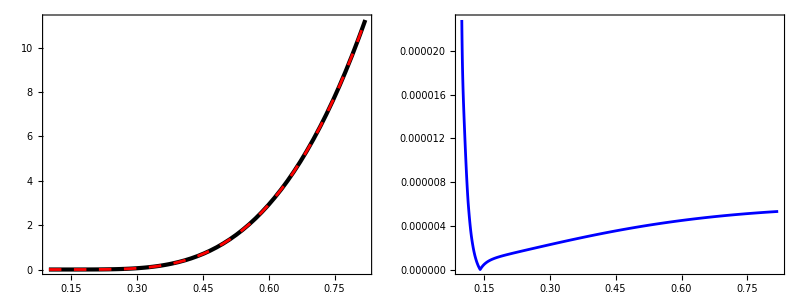

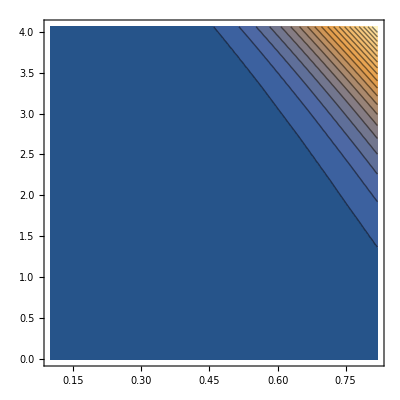

```mathematica
m = 1.11568*GeVinversefm;
dof = 2.0;
θ=1.0;
N30Integrand[T_,μB_,pbar_]:=(dof*(T)^5)/(2.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(2/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
N30GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^5)/(2.0*Pi^2)*(pbar)^-1*((pbar)^2+(m/T)^2)^(2/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

N30=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[N30Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N30Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*N30GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N30=Interpolation[N30];
N30Gauss=Interpolation[N30Gauss];
GraphicsGrid[{{Plot[{N30[T,μBmin],N30Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N30[T,μBmin]-N30Gauss[T,μBmin])]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{N30[T,μBmax],N30Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N30[T,μBmax]-N30Gauss[T,μBmax])/N30Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(N30[T,μB]-N30Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(N30[T,μB]-N30Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Omega

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

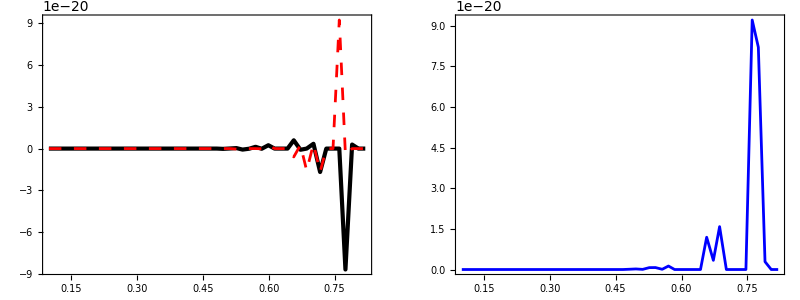

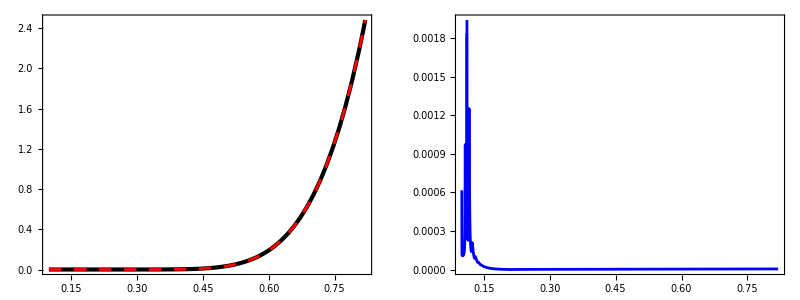

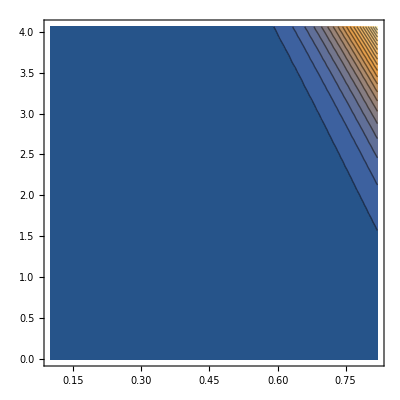

```mathematica
m = 1.67243*GeVinversefm;
dof = 4.0;
θ=1.0;
N30Integrand[T_,μB_,pbar_]:=(dof*(T)^5)/(2.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(2/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
N30GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^5)/(2.0*Pi^2)*(pbar)^-1*((pbar)^2+(m/T)^2)^(2/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

N30=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[N30Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N30Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*N30GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N30=Interpolation[N30];
N30Gauss=Interpolation[N30Gauss];
GraphicsGrid[{{Plot[{N30[T,μBmin],N30Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N30[T,μBmin]-N30Gauss[T,μBmin])]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{N30[T,μBmax],N30Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N30[T,μBmax]-N30Gauss[T,μBmax])/N30Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(N30[T,μB]-N30Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(N30[T,μB]-N30Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Omega2250

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

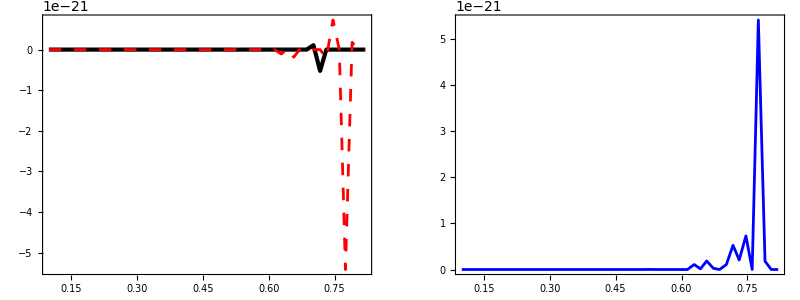

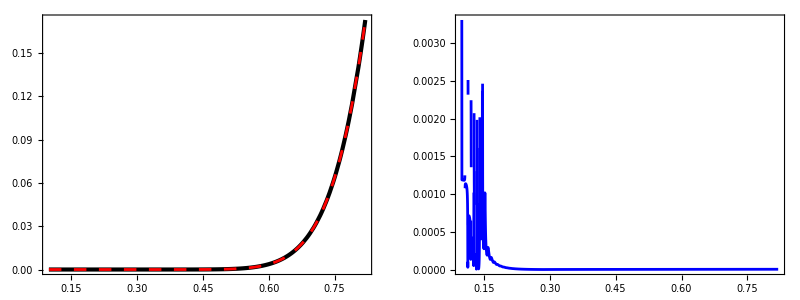

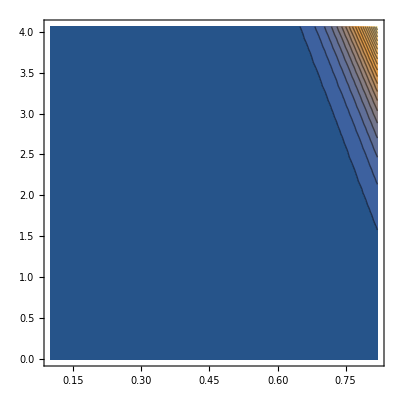

```mathematica
m = 2.25200*GeVinversefm;
dof = 4.0;
θ=1.0;
N30Integrand[T_,μB_,pbar_]:=(dof*(T)^5)/(2.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(2/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
N30GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^5)/(2.0*Pi^2)*(pbar)^-1*((pbar)^2+(m/T)^2)^(2/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

N30=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[N30Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N30Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*N30GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N30=Interpolation[N30];
N30Gauss=Interpolation[N30Gauss];
GraphicsGrid[{{Plot[{N30[T,μBmin],N30Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N30[T,μBmin]-N30Gauss[T,μBmin])]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{N30[T,μBmax],N30Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N30[T,μBmax]-N30Gauss[T,μBmax])/N30Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(N30[T,μB]-N30Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(N30[T,μB]-N30Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```